# Fitting With DNNs

Markus van Almsick, WRI

## Creating Data

```mathematica
coeff={0.3,-1,2.1,0.6,0.0,1.3,-0.5,0.9};
```

```mathematica
trainingData = Table[Join[RandomReal[{-1,1},{6}],RandomInteger[{0,1},{2}]],{50}];
```

```mathematica
trainingResults=trainingData.coeff+RandomReal[NormalDistribution[0,0.2],Length[trainingData]];
```

```mathematica
testData = Table[Join[RandomReal[{-1,1},{6}],RandomInteger[{0,1},{2}]],{20}];
```

```mathematica
testResults=testData.coeff+RandomReal[NormalDistribution[0,0.2],Length[testData]];
```

## Predict

```mathematica
p=Predict[Thread[trainingData->trainingResults],Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
pm=PredictorMeasurements[p,Thread[testData->testResults]]
```

PredictorMeasurementsObject[…]

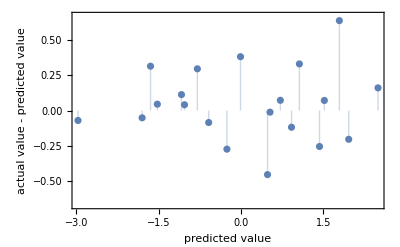
{-Graphics-,0.256085}

```mathematica
pm /@ {"ResidualPlot","StandardDeviation"}
```

## NeuralNetwork

```mathematica
network = NetChain[
{LinearLayer[32],
ElementwiseLayer["Sigmoid"],
LinearLayer[20],
LinearLayer[1]
},
"Input"->8,
"Output"->1
]
```

NetChain[<>]

```mathematica
trainedNetwork=NetTrain[network,Thread[trainingData->Transpose[{trainingResults}]],
ValidationSet->Thread[testData->Transpose[{testResults}]]]
```

NetChain[<>]

```mathematica
predictedTestResults=Map[trainedNetwork,testData]⟦All,1⟧
```

{-0.90791,0.591984,1.73942,2.54163,-2.86316,-1.17891,-1.97656,-1.72723,-0.041723,-0.316478,0.687672,0.474281,1.44566,1.07859,0.948317,-1.2427,1.58254,-0.75323,-1.5755,1.91799}

StandardDeviation:

```mathematica
Sqrt@Mean[(predictedTestResults-testResults)^2]
```

0.28497